## Prime visibility

```mathematica
SetDirectory[NotebookDirectory[]];
primes=Table[Prime[x],{x,10000}];
```

```mathematica
horizontalQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] < ts[[a]] && ts[[x]] < ts[[b]],result=True,result=False;Return[False]],
		{x,a+1,b-1}
	];
	Return[result]
]
```

```mathematica
visibleQ[a_Integer, b_Integer, ts_List]:=Block[{result=True},
	Do[
		If[ts[[x]] >= ts[[a]]+(ts[[b]]−ts[[a]])(x−a)/(b−a),result=False;Return[]],
		{x,a+1,b-1}
	];
	result
]
```

```mathematica
naturalVisibilityLinks[vals_List]:=Block[{visibles,l},
SetSharedVariable[visibles];
visibles={};
l=Length@vals;
ParallelDo[
Scan[
If[visibleQ[i,#,vals],AppendTo[visibles,i->#]]&,
Range[i+1,l]
],
{i,1,l-1}];
visibles
]
```

```mathematica
horizontalVisibilityLinks[vals_List]:=Block[{visibles},
visibles={};Do[
Do[
If[horizontalQ[i,j,vals],AppendTo[visibles,i->j],Null],
{j,i+1,Length@vals}
],
{i,1,Length@vals-1}];
visibles
]
```

```mathematica
plotModel[count_, len_]:=Block[
{countrel,nlm,x,C,γ},
countrel=Table[{x,Lookup[count,x]/len}, {x,Keys[count]}];
nlm=NonlinearModelFit[countrel,C x^-γ,{C,γ},x];
{
{#1,Differences[#2][[1]]/2}&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]],
Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],
Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
}
]
```

```mathematica
plotLinearModel[count_, len_]:=Block[
{countrel,nlm,x,points},
countrel=Table[{x,Lookup[count,x]/len}, {x,Keys[count]}];
points=Log@countrel;
lm=LinearModelFit[points,x,x];
Show[
ListPlot[points,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large,AspectRatio->0.8
]
]
```

```mathematica
naturalVisibility[series_]:=Block[{visibles},
	visibles={};
	Do[
		Do[
			If[visibleQ[i,j,series],AppendTo[visibles,i->j],Null],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

## Natural Visibility Graph

```mathematica
naturalLinks=naturalVisibility[primes];
```

## Graph

```mathematica
natLinks=Table[Prime[i[[1]]]->Prime[i[[2]]],{i,naturalLinks}]
```

{2→3,2→5,2→7,2→11,2→17,2→23,2→29,2→37,2→41,2→53,2→59,2→67,2→71,2→79,2→83,2→89,2→97,2→101,806633,104651→104677,104659→104677,104677→104681,104677→104693,104677→104701,104681→104683,104681→104693,104681→104701,104683→104693,104693→104701,104701→104707,104707→104711,104707→104717,104707→104723,104707→104729,104711→104717,104717→104723,104723→104729}
 |  |  |  |

```mathematica
naturalGraph=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count=VertexDegree[natLinks]//Counts;
```

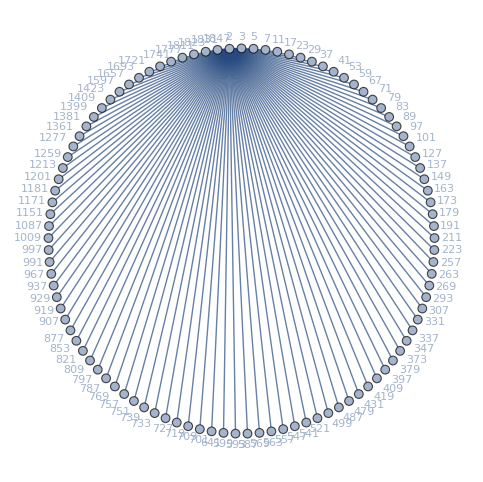

```mathematica
Graph[natLinks[[;;100]], DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"]
```

```mathematica
seenByTwo=Select[natLinks,First[#]==2&][[All,2]]
```

```mathematica
Select[natLinks,First[#]==3&][[All,2]]==seenByTwo[[2;;]]
```

False

```mathematica
DumpSave["2-prime-links.mx",natLinks];
```

## Model fit

```mathematica
nlm=NonlinearModelFit[Table[{x,count[x]},{x,Keys[count]}],b x^-a,{a,b},x]
```

FittedModel[3087.23/x^1.11651]

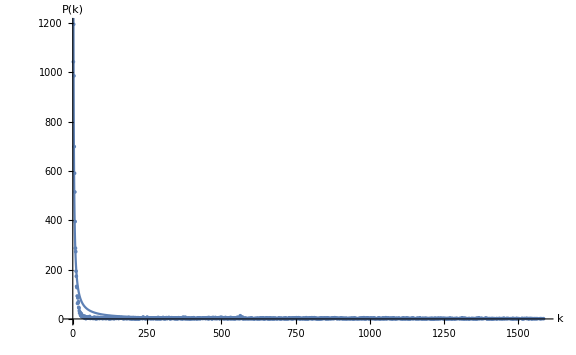

```mathematica
vis2=Show[
ListPlot[Table[{x,count[x]},{x,Keys[count]}],PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-2.eps",vis2];
```

## Mean degree

```mathematica
degree=VertexDegree[naturalGraph]//Mean//N
```

161.334

## Record result

```mathematica
Flatten[{"visibility", degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]
```

{visibility,161.334,1.11651 ± 0.0262405,3087.23 ± 120.517}

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igh2=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh2];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→3629,3→2482,4→1501,5→879,7→354,6→536,8→234,9→136,14→11,11→59,13→15,12→39,10→105,15→10,16→4,25→1,17→2|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

{{2,3629/9999},{3,2482/9999},{4,1501/9999},{5,293/3333},{7,118/3333},{6,536/9999},{8,26/1111},{9,136/9999},{14,1/909},{11,59/9999},{13,5/3333},{12,13/3333},{10,35/3333},{15,10/9999},{16,4/9999},{25,1/9999},{17,2/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

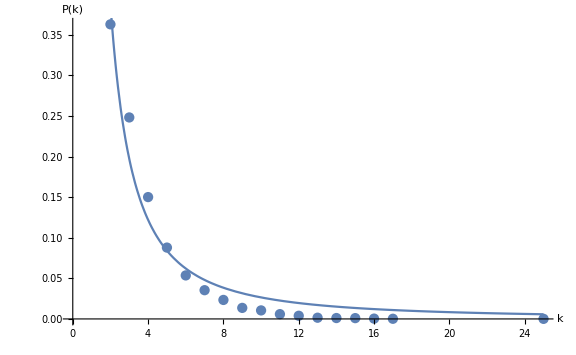

```mathematica
hvis2=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-2.eps",hvis2];
```

## Mean degree

```mathematica
degree=VertexDegree[igh2]//Mean//N;
```

## Record result

```mathematica
(*AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];*)
```

## Return result

```mathematica
results
```

{}